Задача 3.

## а) Да се състави таблицата (x_i,f(x_i)), където x_i=10+b+i(0.3), i=OverBar[0, 10], а f(x) е функцията от Задача 1.

```mathematica
xi = Table[17.+i*0.3,{i,0,10}]
```

{17.,17.3,17.6,17.9,18.2,18.5,18.8,19.1,19.4,19.7,20.}

```mathematica
f[x_]:= (-405Cos[x] + x^3  + 23)/(9 - x^2);
yt = f[xi]
```

{-18.0266,-17.886,-17.778,-17.7342,-17.7788,-17.9268,-18.1836,-18.545,-18.9983,-19.5236,-20.0965}

```mathematica
n = Length[xi]
points = Table[{xi[[i]],yt[[i]]},{i,1,n}]
```

11

Отговор:

{{17.,-18.0266},{17.3,-17.886},{17.6,-17.778},{17.9,-17.7342},{18.2,-17.7788},{18.5,-17.9268},{18.8,-18.1836},{19.1,-18.545},{19.4,-18.9983},{19.7,-19.5236},{20.,-20.0965}}

## б) Пресметнете ∫f(x)ⅆx=∫_17^20 f(x)ⅆx по целия интервал получен в а) по формулата на левите правоъгълници, използвайки получените точки.

#### Оценка на грешката:

Теоретична грешка - намираме M1:

```mathematica
f'[x_]:= (-(-405 x^2-3645)Sin[x]-810x Cos[x]- x^4  + 23 x^2+46 x)/((9 - x^2)^2);
```

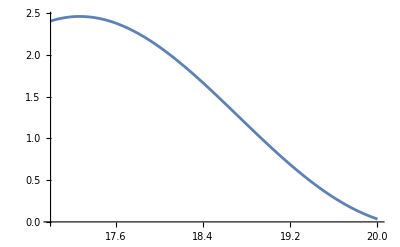

```mathematica
Plot[Abs[(-(-405 x^2-3645)Sin[x]-810x Cos[x]- x^4  + 23 x^2+46 x)/((9 - x^2)^2)],{x,17,20}]
```

```mathematica
M1 = Abs[f'[17.3]]
```

0.43368

```mathematica
R1 = (b-a)^2/(2n)*M1
```

0.177414

Истинска грешка:

```mathematica
Abs[I1-Itochno]
```

0.267106

```mathematica
f[x_]:= (-405Cos[x] + x^3  + 23)/(9 - x^2);
Itochno = ∫_17^20 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 17.;b = 20.;
n = 11;
h = (b-a)/n;
 I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[17.3]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приближената стойност по метода на левите правоъгълници е ", I1]
Print["Точната стойност е                                        ", Itochno]
Print["Теоретичната грешка по метода на левите правоъгълници е ", R1]
Print["Истинската грешка е                                     ", Abs[I1-Itochno]]
```

Мрежата е със стъпка h = 0.272727 и брой подинтервали n = 11

Отговор:

Приближената стойност по метода на левите правоъгълници е -54.7393

Точната стойност е                                        -55.0064+0. ⅈ

Теоретичната грешка по метода на левите правоъгълници е 0.177414

Истинската грешка е                                     0.267106

в) Каква е грешката на полученото приближение в б)?

Отговор:

Мрежата е със стъпка h = 0.272727 и брой подинтервали n = 11

Приближената стойност по метода на левите правоъгълници е -54.7393

Точната стойност е                                        -55.0064+0. ⅈ

Теоретичната грешка по метода на левите правоъгълници е 0.178307

Истинската грешка е                                     0.267106

г) Колко би трябвало да са подинтервалите, ако се иска да се достигне грешка 0.000001 със същата квадратурна формула?

```mathematica
Clear[n]
Reduce[(b-a)^2/(2n)*M1<=10^-6, n]//N
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0.||n≥461374.

```mathematica
f[x_]:=(-405Cos[x] + x^3  + 23)/(9 - x^2);
Itochno = ∫_17^20 f[x]ⅆx//N ;(*за сравнение с нашите резултати*)
a = 17.;b = 20.;
n=461374;
h = (b-a)/n;
I1 = h*∑_(i=0)^(n-1) f[a+i*h]//N;
M1 = Abs[f'[17.3]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка h = ", h, " и брой подинтервали n = ",n]
Print["Приближената стойност по метода на левите правоъгълници е ", I1]
Print["Точната стойност е                                        ", Itochno]
Print["Теоретичната грешка по метода на левите правоъгълници е ", R1]
Print["Истинската грешка е                                     ", Abs[I1-Itochno]]
```

Отговор:

Мрежата е със стъпка h = 6.50232×10^-6 и брой подинтервали n = 461374

Приближената стойност по метода на левите правоъгълници е -55.0064

Точната стойност е                                        -55.0064+0. ⅈ

Отговор: Приближената стойност става равна на точната.

Теоретичната грешка по метода на левите правоъгълници е 4.22988×10^-6

Истинската грешка е                                     6.7296×10^-6

д) Може ли по построената таблица да се използва квадратурната формула на Симпсън за изчисляване на интеграла ∫f(x)ⅆx по целия интервал получен в а)? Обосновете отговора си.

Квадратурната формула на Симпсън не може да се използа, тъй като броят на подинтервалите n=11 е нечетно число.